## Structural complexity of functional response models - Part 2

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/marknovak/Git/general-functional-responses/code/Mathematica

```mathematica
"/Users/marknovak/Git/general-functional-responses/code/Mathematica"
```

/Users/marknovak/Git/general-functional-responses/code/Mathematica

### Preliminaries

SC_2= -Log_ef(x|(Θ̂)_x)+k/2 Log_e(n/(2 π))+Log_e∫_Θ √(det I(Θ))ⅆΘ + o(1)
The first term is the likelihood. 
The second term is dependent on parameter count (k) and sample size (n).
The third term containing I(Θ), the Expected Fisher Information Matrix, reflects the model's flexibility.
The flexibility term by itself can only be compared between models having the same number of parameters.

#### Load results of "FisherMatrix-1_Compute.nb”

Pick the output that has been successfully computed :

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3_NInt"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3_aNInt"];
```

### Second Term dependence on k and n

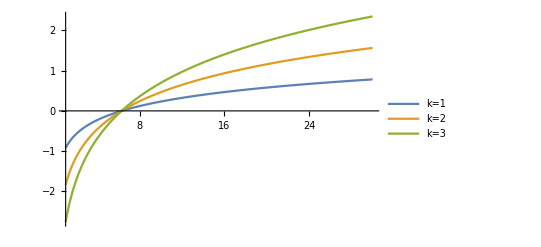
-Graphics-Sample size (n)Parameter complexity

```mathematica
AltLabel1="k";
p1=Labeled[Plot[Evaluate@Table[k/2 Log[n/(2 π)],{k,1,3}],{n,1,30},
PlotLegends->Placed[{"k=1","k=2","k=3"},Above]],
{Style["Sample size (n)"],Style["Parameter complexity"]},{Bottom,Left},
RotateLabel->True,
Spacings->{1, 0},
BaseStyle->{FontFamily->"Arial",12},
LabelStyle->{FontFamily->"Arial"},
ImageSize->Medium]
Export["results/FisherMatrix-2_Output_ParameterComplexity.pdf",p1];
```

### Third term - Flexibility - Non-truncated λ

```mathematica
NInts={NIntH1,NIntR,NIntHV,NIntH2,NIntAG,NIntBD,NIntCM,NIntAA}
Labels={"H1","R","HV","H2","AG","BD","CM","AA"};
gNInts={NInts[[{1,2}]],
NInts[[{3,4,5}]],
NInts[[{6,7,8}]]
};
rNInts={NInts[[{1,2}]]/NInts[[1]],
NInts[[{3,4,5}]]/NInts[[3]],
NInts[[{6,7,8}]]/NInts[[6]]
};
(* Export["results/FisherMatrix-2_Output_logNIntegrals.txt",{Νvals,Pvals,Labels,NInts,rNInts}]; *)
```

{6.71492,6.22451,11.7166,11.1972,10.4422,14.433,14.7811,15.5271}

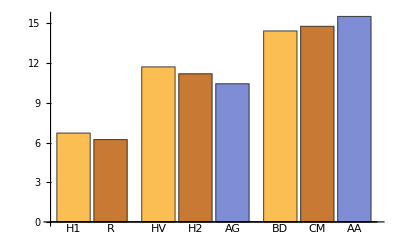
-Graphics-ModelFlexibility

```mathematica
AltLabel2="LN∫_Θ √(det  I (θ))ⅆθ";
lNInts=TakeList[MapIndexed[Labeled[#,Labels[[#2[[1]]]]]&,Flatten@gNInts],Length/@gNInts];
bc1=Labeled[BarChart[lNInts],
{Style["Model"],Style["Flexibility"]},{Bottom,Left},
RotateLabel->True,
Spacings->{0.4, 1},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"},
ImageSize->Medium]
Export["results/FisherMatrix-2_Output_Complexity_absolute_NonTrunc.pdf",bc1];
```

### Third term - Flexibility - Truncated λ

```mathematica
NInts={NIntH1Trunc,NIntRTrunc,NIntHVTrunc,NIntH2Trunc,NIntAGTrunc,NIntBDTrunc,NIntCMTrunc,NIntAATrunc}
Labels={"H1","R","HV","H2","AG","BD","CM","AA"};
gNInts={NInts[[{1,2}]],
NInts[[{3,4,5}]],
NInts[[{6,7,8}]]
};
rNInts={NInts[[{1,2}]]/NInts[[1]],
NInts[[{3,4,5}]]/NInts[[3]],
NInts[[{6,7,8}]]/NInts[[6]]
};
(* Export["results/FisherMatrix-2_Output_logNIntegrals.txt",{Νvals,Pvals,Labels,NInts,rNInts}]; *)
```

{3.8831,3.83281,6.4934,5.76324,5.89872,5.49278,6.10262,8.05252}

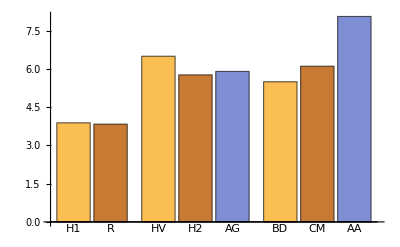
-Graphics-ModelFlexibility

```mathematica
AltLabel2="LN∫_Θ √(det  I (θ))ⅆθ";
lNInts=TakeList[MapIndexed[Labeled[#,Labels[[#2[[1]]]]]&,Flatten@gNInts],Length/@gNInts];
bc1=Labeled[BarChart[lNInts],
{Style["Model"],Style["Flexibility"]},{Bottom,Left},
RotateLabel->True,
Spacings->{0.4, 1},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"},
ImageSize->Medium]
Export["results/FisherMatrix-2_Output_Complexity_absolute_Trunc.pdf",bc1];
```

### Partial numeric Integration - Non-truncated λ

Fix ' a', integrate square root of Expected Fisher Information Matrix over remaining parameters , and take natural log.

```mathematica
ParmRangeB=Drop[ParmRangeA,1];
precgoal=2;
pnk1=Plot[{
aNIntH1,
aNIntR
},
{a,0.01,1},
PlotLegends->Placed[{"H1","R"},Above]];
```

```mathematica
pnk2=Plot[{
aNIntHV,
aNIntH2[a],
aNIntAG[a]
},
{a,0.01,1},
PlotLegends->Placed[{"HV","H2","AG"},Above]];
```

```mathematica
pnk3=Plot[{
aNIntBD[a],
aNIntCM[a],
aNIntAA[a]
},
{a,0.01,1},
PlotLegends->Placed[{"BD","CM","AA"},Above]];
```

```mathematica
pn=Labeled[GraphicsRow[{pnk1,pnk2,pnk3},ImageSize->Large],{Style["Attack rate"],Style["LN∫_Θ √(det  I (θ))ⅆθ"]},{Bottom,Left},RotateLabel->True,Spacings->{3, 0},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"}]
Export["results/FisherMatrix-2_Output_partial_numeric_a_NonTrunc.pdf",pn];
```

-Graphics-Attack rateLN∫_Θ √(det  I (θ))ⅆθ

### Partial numeric Integration - Truncated λ

Fix ' a', integrate square root of Expected Fisher Information Matrix over remaining parameters , and take natural log.

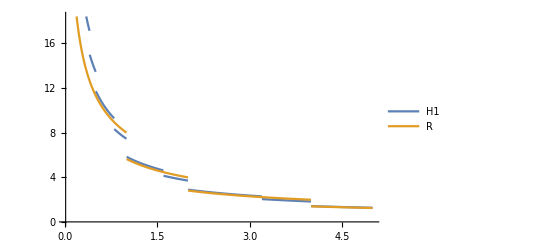

```mathematica
ParmRangeB=Drop[ParmRangeA,1];
precgoal=2;
pnk1T=Plot[{
aNIntH1Trunc,
aNIntRTrunc
},
{a,0.01,5},
PlotLegends->Placed[{"H1","R"},Above]]
```

```mathematica
aNIntH1Trunc
```

√(Boole[0≤2 a≤256]/(12 a)+Boole[0≤4 a≤256]/(3 a)+(2 Boole[0≤8 a≤256])/(3 a)+(5 Boole[0≤10 a≤256])/(12 a)+(4 Boole[0≤16 a≤256])/(3 a)+(5 Boole[0≤20 a≤256])/(6 a)+(8 Boole[0≤32 a≤256])/(3 a)+(5 Boole[0≤40 a≤256])/(3 a)+(16 Boole[0≤64 a≤256])/(3 a)+(10 Boole[0≤80 a≤256])/(3 a)+(32 Boole[0≤128 a≤256])/(3 a)+(20 Boole[0≤160 a≤256])/(3 a)+(64 Boole[0≤256 a≤256])/(3 a)+(40 Boole[0≤320 a≤256])/(3 a)+(64 Boole[0≤512 a≤256])/(3 a)+(80 Boole[0≤640 a≤256])/(3 a)+(160 Boole[0≤1280 a≤256])/(3 a))

```mathematica
aNIntRTrunc
```

√(Boole[0≤2 a≤256]/(4 a)+Boole[0≤4 a≤256]/(2 a)+Boole[0≤8 a≤256]/a+(2 Boole[0≤16 a≤256])/a+(4 Boole[0≤32 a≤256])/a+(8 Boole[0≤64 a≤256])/a+(16 Boole[0≤128 a≤256])/a+(32 Boole[0≤256 a≤256])/a)

```mathematica
Νvals
```

{2,4,8,16,32,64,128,256}

```mathematica
Pvals
```

{1,2,5}

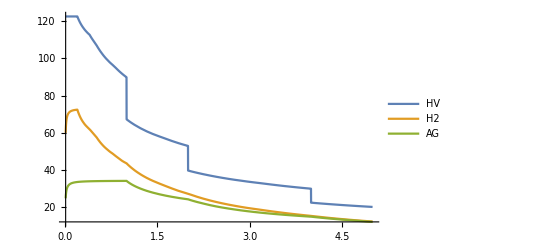

```mathematica
pnk2T=Plot[{
aNIntHVTrunc[a],
aNIntH2Trunc[a],
aNIntAGTrunc[a]
},
{a,0.01,5},
PlotLegends->Placed[{"HV","H2","AG"},Above]]
```

```mathematica
pnk3T=Plot[{
aNIntBDTrunc[a],
aNIntCMTrunc[a],
aNIntAATrunc[a]
},
{a,0.01,0.1},
PlotLegends->Placed[{"BD","CM","AA"},Above]]
```

```mathematica
pnT=Labeled[GraphicsRow[{pnk1T,pnk2T,pnk3T},ImageSize->Large],{Style["Attack rate"],Style["LN∫_Θ √(det  I (θ))ⅆθ"]},{Bottom,Left},RotateLabel->True,Spacings->{3, 0},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"}]
Export["results/FisherMatrix-2_Output_partial_numeric_a_Trunc.pdf",pnT];
```

-Graphics-Attack rateLN∫_Θ √(det  I (θ))ⅆθ

## Compare non-truncated and truncated Sqrt(Det(FIM)) before integrating over parameters

```mathematica
DetH1NoTrunc=DetEFisherTrunc[FisherH1Poiss,H1,0,Infinity,subs];
```

NOTE: If we don’t truncate things then everything is identical, but things definitely change upon reducing λmax to Max[Nvals].

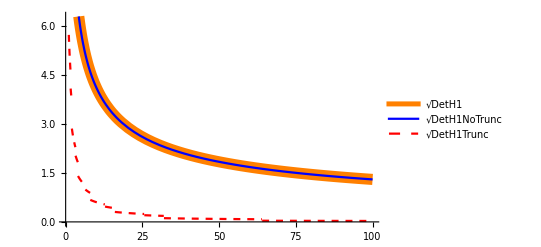

```mathematica
pH1=Plot[{Sqrt[DetH1],Sqrt[DetH1NoTrunc],Sqrt[DetH1Trunc]},{a,0,100},
PlotStyle->{{Orange,Thickness[0.02]},{Blue},{Red,Dashed}},
PlotLegends->"Expressions"]
```

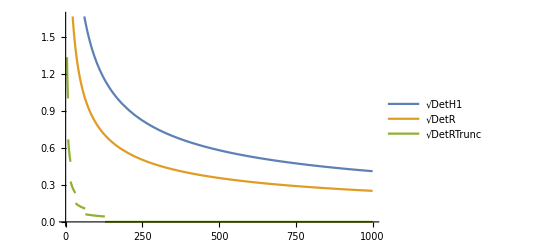

```mathematica
pR=Plot[{Sqrt[DetH1],Sqrt[DetR],Sqrt[DetRTrunc]},{a,0,1000},
PlotLegends->"Expressions"]
```

```mathematica
p3Dk1=GraphicsColumn[{pH1,pR},ImageSize->Large];
Export["results/FisherMatrix-2_Output_preIntegration-3Dk1.jpeg",p3Dk1];
```

```mathematica
pHV=Plot3D[{Sqrt[DetHV],Sqrt[DetHVTrunc]},{a,0,10},{m,0,5},AxesLabel->Automatic,
PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
pH2=Plot3D[{Sqrt[DetH2],Sqrt[DetH2Trunc]},{a,0,10},{h,0,5},AxesLabel->Automatic,
PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
pAG=Plot3D[{Sqrt[DetAG],Sqrt[DetAGTrunc]},{a,0,10},{h,0,5},AxesLabel->Automatic,
PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
p3Dk2=GraphicsColumn[{pHV,pH2,pAG},ImageSize->Large];
Export["results/FisherMatrix-2_Output_preIntegration-3Dk2.jpeg",p3Dk2];
```